This project looks to explore numerical multiway systems through visualization, and analyze relationships and patterns with more advanced functions. Afterwards, the project moves to focus on a relationship between the Catalan numbers and Dyck paths. Multiway systems were created, and custom rendering was done to generate the Dyck path based on edges. The goal of this project was to visualize Dyck graphs, and then add modifications, such as blocking a certain edge or moving the diagonal higher, and analyze any possible generalizations made from the modifications.

## Introduction

Multiway systems are systems generated by a set of rules that are recursively applied to all of the outputs. Here’s a sample systematic output from a rule

```mathematica
s ↦ {Subscript[f, 1][s], Subscript[f, 2][s]}
```

Symbolic multiway graph

```mathematica
ResourceFunction["NestGraphTagged"][n↦{Subscript[f,1][n],Subscript[f,2][n]},s,3,EdgeLabels->(DirectedEdge[_,_,i_]:>Placed[Text@({"f_1","f_2"}[[i]]),0.5]),AspectRatio->.4,
"StateLabeling"->True,"FormattingFunction"->(Style[Text[#],9,Black]&),
FormatType->StandardForm,
ImageSize->680]
```

-Graphics-

Multiway systems can have a myriad of applications, including studying states in games and puzzles, such as Othello, or more theoretical aspects such as its use in the Wolfram Physics Project.

#### General Observations

Generally, with a linear or multiplicative multiway systems, merging behavior can be predicted by the various constant values.

Consider a system of the form

```mathematica
n |-> {an, n + b}
```

With this, we can predict the initial grid like pattern that arises, at least from the lower level branches.

Multiway system subgraph with symbolic values

```mathematica
Graph[With[{g=ResourceFunction["NestGraphTagged"][x|->Expand[{5x,x+3}],{n},6,"StateLabeling"->True]},Subgraph[g,First/@First[FindCycle[UndirectedGraph[g],{8}]]]]]
```

-Graphics-

where the left hand side will always have  sides, and the right hand side has 2 sides, resulting in ()-gons, as explained by Stephen Wolfram’s work “Multicomputation with Numbers: The Case of Simple Multiway Systems”. However, there are some exceptions to this behavior.  
For example, consider the rule set

```mathematica
n|->{2n, n+5}
```

The resulting graph ends up with one heptagon, with the remaining grids being pentagons. Every pentagon is also in the format of the generalized ()-gon as explained above, which is trivial to see.

Plot of the new multiway system with the above rules

```mathematica
ResourceFunction["NestGraphTagged"][n↦{2n, n+5},{1},7,"StateLabeling"->True, PlotLegends->TraditionalForm/@{2n, n+5}]
```

-Graphics-

Zooming in on the heptagon subset, we see

Subgraph of the heptagon

```mathematica
Graph[With[{g=ResourceFunction["NestGraphTagged"][x|->Expand[{2x,x+5}],{1},6,"StateLabeling"->True]},Subgraph[g,First/@First[FindCycle[UndirectedGraph[g],{7}]]]]]
```

-Graphics-

Conveniently,

and this can easily be seen as true, as an integer  would exist through Fermat’s Little Theorem, since  and  are relatively prime. This suggests the only irregularities from an otherwise uniform lattice grid would be multiples of the order that make this equation true.

Experimenting with more functions here, we see interesting relationships.

Totient function and resulting graph with

```mathematica
totient[n_Integer] := Length[ResourceFunction["CoprimeIntegerList"][n]]
ResourceFunction["NestGraphTagged"][n↦{totient[n], n - totient[n] },{1138},20,"StateLabeling"->True,PlotLegends->TraditionalForm/@{Totient[n], Common[n]}]
```

-Graphics-

For any number , there seems to be an unusually high convergence to a power of two, suggesting some sort of lower bound (possibly logistic or exponential?) that exists.

## Dyck Paths

Dyck paths are lattice paths from  to  that do not pass above the diagonal (). For example, here’s an Dyck path where

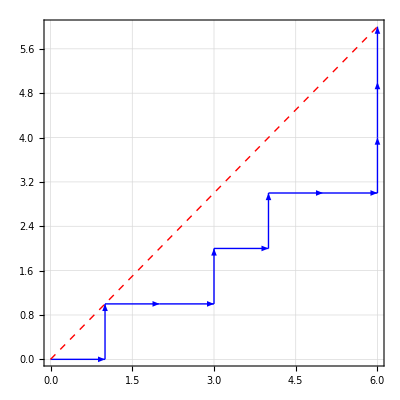

From any given point, a path can be generated by the map

```mathematica
{x, y} |-> {{x+1, y}, {x,y+1}}
```

or simply right and up “moves”. However, to make this path into a Dyck path, we will have to consider the restriction of the diagonal. To turn this into a multiway graph, I recursively build the graph by finding the next edge with the rule described above.

```mathematica
dyckNext[lst_List, n_Integer] := Module[{x := Last[lst][[2]][[1]], y := Last[lst][[2]][[2]]},
	Which[
		Length[lst] == 0, {{{0, 0}, {1, 0}}},
		x==n, {{{x, y}, {x, y + 1}}},
		x > y, {{{x, y}, {x + 1, y}}, {{x, y}, {x, y + 1}}}, 
		True,{{{x, y}, {x + 1, y}}}
	]
]
```

The which above hard codes the empty set case and the ending case (i.e., all up), and checks the ending lattice point of the last edge to consider how many of the paths would be valid.

Generates all the next possible edges from the last move of the step

```mathematica
dyckNext[{}, 6]
dyckNext[{{{0, 0}, {1, 0}}}, 6]
dyckNext[{{{0, 0}, {1, 0}}, {{1,0},{1,1}}}, 6]
```

{{{0,0},{1,0}}}

{{{1,0},{2,0}},{{1,0},{1,1}}}

{{{1,1},{2,1}}}

This function generates the Dyck path from the list of edges provided.

Generates the graph from a list of edges

```mathematica
dyckGraph[lst_List, n_Integer] := Graphics[
	{Blue, Arrow[Partition[Flatten[lst, 1], 2]], 
	Red, Dashed, Line[{{0, 0}, {n, n}}]}, 
	Frame -> True,
	GridLines -> Automatic,
	ImageSize -> Full
]
```

We test this, as well as a function to generate random Dyck Paths below.

Generates and displays a Dyck path on a 6×6-grid

```mathematica
generateDyckPath[n_Integer] := Module[{lst = {}},
	Last[
		Table[
			AppendTo[lst, RandomChoice[dyckNext[lst, n]]], {i, Range[2*n]}
		]
	]
]
```

```mathematica
dyckGraph[generateDyckPath[6], 6]
```

-Graphics-

In preparation of creating our multiway system, the display function will be updated to clear up some clutter.

Smaller display function to not cloud up the multiway graphs

```mathematica
dyckGraph[lst_List, n_Integer] := Graphics[
	{Blue, Arrow[Partition[Flatten[lst, 1], 2]], 
	Red, Dashed, Line[{{0, 0}, {n, n}}]}, 
	GridLines -> {Range[0, n, 1], Range[0, n, 1]},
	ImageSize -> 15
]
```

Now, to actually create the multiway system, we utilize the function “MultiwaySystem” from the Wolfram Research Repository.

Function to create the multiway system for Dyck graphs

```mathematica
showGraph[graphs_List, n_Integer, level_Integer] := ResourceFunction["MultiwaySystem"][
	<|"StateEvolutionFunction" -> Function[list, Append[list, #] & /@ dyckNext[list, n]],
	|>,
	{graphs}, level, "StatesGraph", 
	"StateRenderingFunction"->(Inset[dyckGraph[#2, n], #1]&)
]
```

and we can call it below to generate a sample Dyck path multiway system.

Generates a Dyck graph

```mathematica
n=4;
showGraph[{}, n, 2*n]
```

-Graphics-

Here’s an interactive you can play around with for both  and the level. It might be a bit lag inducing, so be warned.

Visual of Dyck path recursive chain and steps for varying sizes of grids

```mathematica
Dynamic[n];
n=4;
Slider[Dynamic[n], {1, 6, 1}]
Dynamic[ListAnimate[Table[showGraph[{}, n, moves], {moves, Range[2 * n]}], AnimationRunning->False]]
```

Now, let’s take a look at the number of Dyck paths for each value of .

All valid and the number of Dyck paths for 1×1 to 6×6 grids.

```mathematica
Grid[Table[{graph = showGraph[{}, i,  2 * i], "Paths: " <> ToString[VertexCount[graph, _?(Last[#][[2]] == {i, i} &)]]}, {i, 1, 6, 1}]
]
```

-Graphics-

Do the number of paths look familiar? To those well versed in number theory, you should recognize these as the Catalan numbers.

It is well known that the number of Dyck paths for a -grid is equivalent to the -th Catalan number. One visualization of the proof can be shown as such (proof rewritten from Stack Exchange).

Lemma 1. The number of Dyck paths for a -grid is equivalent to , where

-Graphics-

Proof. Let the first time the path touches the diagonal be at , and we know that it must, as at the very least, the Dyck path will end at . Then, if we consider the first part (part in green), we can see that if we were to draw the line , we would effectively get a Dyck path below on a -grid, since it is the first time that it intersects with the line. On the other side, we would end up with an -grid (highlighted in purple). As a result, by considering every possible value of , from  to , we can split into the sum of two Catalan numbers , which gets us our desired summation above.

To get an interactive visualization, we need to create a few functions, as well as updating a few old ones (explanation later), in preparation for the next section.

Updated functions:

Updated functions to add restrictions (explained later)

```mathematica
dyckNext[lst_List, n_Integer, resCol_List:Range[0, 10], badEdges_List : {}] := Module[{x, y},
	x = If[Length[lst] != 0, Last[lst][[2]][[1]], 0];
	y = If[Length[lst] != 0, Last[lst][[2]][[2]], 0];
	If[Length[resCol] == 0, resCol=Range[0, n]];
	Select[{{{x, y}, {x + 1, y}}, {{x, y}, {x, y + 1}}}, Length[resCol] >= #[[2]][[1]] + 1 && #[[2]][[2]]<= resCol[[#[[2]][[1]] + 1]] && #[[2]][[1]] <= n && !MemberQ[badEdges, #]&]
]
generateDyckPath[n_Integer, resCol_List:Range[0, 10], badEdges_List : {}] :=  Module[{lst = {}},
	Last[Table[AppendTo[lst, RandomChoice[dyckNext[lst, n, resCol, badEdges]]], {i, Range[2*n]}]]
]
dyckGraph[lst_List, n_Integer, resCol_List:Range[0, 10], badEdges_List : {}] := Graphics[{Blue, Arrow[
	Partition[Flatten[lst, 1], 2]], 
	Red, Dashed, Line[#] & /@ Table[{{i - 1, resCol[[i]]}, {i, resCol[[i + 1]]}}, {i, Range[n]}], Line[#] & /@ badEdges}, 
	GridLines->{Range[0,n, 1], Range[0,n, 1]}, ImageSize->15
]
showGraph[graphs_List, level_Integer, resCol_List: Range[0, 10], badEdges_List:{}] :=ResourceFunction["MultiwaySystem"][
	<|"StateEvolutionFunction" -> Function[list, Append[list, #] & /@ dyckNext[list, n, resCol, badEdges]],
	"StateEquivalenceFunction"->SameQ,|>,
	{graphs},level,"StatesGraph",
	"StateRenderingFunction"->(Inset[dyckGraph[#2, n, resCol, badEdges], #1]&)
]
```

New functions:

```mathematica
dyckGraphVis[lst_List, n_Integer, k_Integer] := Graphics[{Blue, Arrow[
	Partition[Flatten[lst, 1], 2]], 
	Purple, Arrow[Select[Partition[
		Flatten[lst, 1],2], #[[1]][[2]] >= k &] 
	], 
	Green, Arrow[Select[Partition[
		Flatten[lst, 1],2], k >=#[[2]][[1]] > 1&&#[[2]][[2]]<k&]
	],
	Red, Dashed, Line[{{0, 0}, {n, n}}], Line[{{1, 0}, {k, k - 1}}]}, 
	GridLines->{Range[0,n, 1], Range[0,n, 1]}, ImageSize->Medium
]
genVisPath[n_Integer, k_Integer] := Module[{lst = generateDyckPath[k, Range[0, k], Table[{{i, i-1}, {i, i}}, {i, Range[k-1]}]]},
	If[n!=k, Last[Table[AppendTo[lst, RandomChoice[dyckNext[lst, n]]], {i, Range[2*(n-k)]}]], lst]
]
```

Now for a visualization of the recursive proof for the case of  (and yes, there are degenerate cases for  and , meaning one of them is equal to )

Dynamic output of recursive formula of Catalan numbers

```mathematica
n=6;
Dynamic[ListAnimate[Table[dyckGraphVis[genVisPath[n, k], n, k], {k, Range[n]}], AnimationRunning->False]]
```

Alternatively, we can also prove the Catalan numbers with an explicit formula.

Lemma 2. The number of Dyck paths for a -grid is equivalent to , where

Proof. Trivially, the number of paths that travel from  to  with only rights and ups is  We observe that any invalid Dyck path must cross over the diagonal, meaning it must intersect the line  at least once. Flipping the invalid portion of the graph results in a path with only rights and ups that ends at , meaning that the problem simplifies to finding the number of paths to travel from  to , which is  . Subtracting these bad paths from the total number of paths, we get the desired result.

There is a proof for the Catalan numbers iteratively involving generating functions, which will be explained briefly here as well.

## Modifications

Now, we seek to explore modified Dyck graphs and analyze the changes in behavior and number of paths. For example, what happens when our restriction isn’t just a diagonal? What happens if we want to prevent paths from passing a specific edge? What would happen if we didn’t have to strictly travel right or up?

Once again, here is the list of updated functions.

Updated functions to add customizable restrictions

```mathematica
dyckNext[lst_List, n_Integer, resCol_List:Range[0, 10], badEdges_List : {}] := Module[{x, y},
	x = If[Length[lst] != 0, Last[lst][[2]][[1]], 0];
	y = If[Length[lst] != 0, Last[lst][[2]][[2]], 0];
	If[Length[resCol] == 0, resCol=Range[0, n]];
	Select[{{{x, y}, {x + 1, y}}, {{x, y}, {x, y + 1}}}, Length[resCol] >= #[[2]][[1]] + 1 && #[[2]][[2]]<= resCol[[#[[2]][[1]] + 1]] && #[[2]][[1]] <= n && !MemberQ[badEdges, #]&]
]
generateDyckPath[n_Integer, resCol_List:Range[0, 10], badEdges_List : {}] :=  Module[{lst = {}},
	Last[Table[AppendTo[lst, RandomChoice[dyckNext[lst, n, resCol, badEdges]]], {i, Range[2*n]}]]
]
dyckGraph[lst_List, n_Integer, resCol_List:Range[0, 10], badEdges_List : {}] := Graphics[{Blue, Arrow[
	Partition[Flatten[lst, 1], 2]], 
	Red, Dashed, Line[#] & /@ Table[{{i - 1, resCol[[i]]}, {i, resCol[[i + 1]]}}, {i, Range[n]}], Line[#] & /@ badEdges}, 
	GridLines->{Range[0,n, 1], Range[0,n, 1]}, ImageSize->15
]
showGraph[graphs_List, n_Integer, level_Integer, resCol_List: Range[0, 10], badEdges_List:{}] := ResourceFunction["MultiwaySystem"][
	<|"StateEvolutionFunction" -> Function[list, Append[list, #] & /@ dyckNext[list, n, resCol, badEdges]],
	"StateEquivalenceFunction"->SameQ,|>,
	{graphs}, level, "StatesGraph", 
	"StateRenderingFunction"->(Inset[dyckGraph[#2, n, resCol, badEdges],#1]&)
]
```

The functions above now have optional parameters resCol and badEdges, where resCol is the list of y-level restrictions by column (by default a range from 0 to  ), and badEdges are a list of any specific edges that we want to ban.

A basic example would be moving up all the resCol values up by one.

```mathematica
Grid[Table[{graph = showGraph[{}, i,  2 * i, Join[Range[i], {i}]], "Nodes: " <> ToString[VertexCount[graph, _?(Last[#][[2]] == {i, i} &)]]}, {i, 2, 7, 1}]]
```

-Graphics-

which would result in getting  for a -grid. This makes intuitively makes sense, as if we were to start with  as our origin, our first move would be to traverse from  to , essentially making it a -grid.

Now what if the column restrictions weren’t uniform?

```mathematica
Row[{graph = showGraph[{}, 6,  2 * 6, {0, 2, 3, 3, 5, 5, 6}], "Nodes: " <> ToString[VertexCount[graph, _?(Last[#][[2]] == {6, 6} &)]]}]
```

-Graphics-

a significant difference from the 132 paths that would have resulted from a uniform change.

Now, we can modify specific edges. For example, let’s prevent the Dyck paths from going through the edge  . What happens then?

Adding (1, 0)--(2, 0) to badEdges

```mathematica
Grid[Table[{graph = showGraph[{}, i,  2 * i, Range[0, i], {{{1, 0}, {2, 0}}}], "Nodes: " <> ToString[VertexCount[graph, _?(Last[#][[2]] == {i, i} &)]]}, {i, 2, 7, 1}]]
```

-Graphics-

We end up with the  -th Catalan number, which is trivial to prove. All the resulting Dyck paths are forced to traverse from   to   to  , resulting in there being a Dyck path from   to  . This also implies blocking off   instead will result us in paths instead.

What if we were to block off ?

Adding (2, 0)--(3, 0) to badEdges

```mathematica
Grid[Table[{graph = showGraph[{}, i,  2 * i, Range[0, i], {{{2, 0}, {3, 0}}}], "Nodes: " <> ToString[VertexCount[graph, _?(Last[#][[2]] == {i, i} &)]]}, {i, 3, 8, 1}]]
```

-Graphics-

Pattern finding these numbers on oeis.org, it turns out these numbers are the coefficients to the polynomial , where  is the generating function of the Catalan numbers as referenced above. Simplifying, we get

so we can see that the number of Dyck paths is equivalent to  for all .

To prove this, we can use complimentary counting, as well as the help of a proof from a Codeforces editorial.

Definition. The -th convolution of the Catalan numbers can be defined as

We can show that the number of paths that start with  rights (i.e.  transformations) is equivalent to the -th convolution of the Catalan numbers.

Lemma 2. The number of Dyck paths on a -grid that start with  right moves is equivalent to .

Proof. Let right and up moves be represented as R and U, respectively. For simplicity’s sake, we start off with defining the problem for . Then the problem becomes isomorphic to RRaUbUc, where a, b, c are valid Dyck paths. We can therefore represent the problem from the equation

and generalized as

We have n right moves and n+k up moves, meaning the total number of paths on a grid is .  Like before, we can use complementary counting and subtract , and simplifying, we get

Now, for an -grid, the number of paths that would go through the edge  (i.e. starting with three right turns) would be . With this, we can complimentary count to finish the proof.

Now, we can look for generalizations. From our work, we can see that the general form for blocking off  would result in   Dyck paths, for a -grid.	 Unfortunately, there aren’t often nicer forms than , as when expanding, there’s a  that can’t easily be factored out. It worked well in this case, since , and half of the terms were even.

Now, let’s try blocking the edge .

Adding (1, 1)--(2, 1) to badEdges

```mathematica
Grid[Table[{graph = showGraph[{}, i,  2 * i, Range[0, i], {{{1, 1}, {2, 1}}}],"Nodes: " <> ToString[VertexCount[graph, _?(Last[#][[2]] == {i, i} &)]]}, {i, 2, 8, 1}]]
```

-Graphics-

which seems to have a closed form , according to oeis.org.

However, blocking  the edge

Adding (2, 1)--(3, 1) to badEdges

```mathematica
Grid[Table[{graph = showGraph[{}, i,  2 * i, Range[0, i], {{{2, 1}, {3, 1}}}],"Nodes: " <> ToString[VertexCount[graph, _?(Last[#][[2]] == {i, i} &)]]}, {i, 3, 8, 1}]]
```

-Graphics-

and

Adding (3, 1)--(4, 1) to badEdges

```mathematica
Grid[Table[{graph = showGraph[{}, i,  2 * i, Range[0, i], {{{3, 1}, {4, 1}}}],"Nodes: " <> ToString[VertexCount[graph, _?(Last[#][[2]] == {i, i} &)]]}, {i, 4, 8, 1}]]
```

-Graphics-

do not map to any rule known so far, suggesting no easy generalization for  edges.

We now move on to vertical edges. For example, what happens when we block the edge ?.

Adding (2, 0)--(2, 1) to badEdges

```mathematica
Grid[Table[{graph = showGraph[{}, i,  2 * i, Range[0, i], {{{2, 0}, {2, 1}}}],"Nodes: " <> ToString[VertexCount[graph, _?(Last[#][[2]] == {i, i} && Last[#][[1]] != {i, i}&)]]}, {i, 2, 7, 1}]]
```

-Graphics-

which happens to have the same progression as blocking off . This is explained by the symmetrical nature of the graph; to go from  to , you either have to travel from  or , and so one of these paths are blocked for both of these progressions. Every path that doesn’t go through  is the same, so the number of paths should be the same.

continuing, we now block off .

Adding (3, 0)--(3, 1) to badEdges

```mathematica
Grid[Table[{graph = showGraph[{}, i,  2 * i, Range[0, i], {{{3, 0}, {3, 1}}}],"Nodes: " <> ToString[VertexCount[graph, _?(Last[#][[2]] == {i, i} && Last[#][[1]] != {i, i}&)]]}, {i, 3, 8, 1}]]
```

-Graphics-

which is equivalent to .

Now, if we were to block out multiple edges, we get more interesting results.

Blocked out two edges that wouldn’t funnel all the paths into one path, namely (2, 2)--(3, 2) and (3, 0)--(3, 1)

```mathematica
Grid[Table[{graph = showGraph[{}, i,  2 * i, Range[0, i], {{{2, 2}, {3, 2}}, {{3, 0}, {3, 1}}}],"Nodes: " <> ToString[VertexCount[graph, _?(Last[#][[2]] == {i, i} && Last[#][[1]] != {i, i}&)]]}, {i, 3, 8, 1}]]
```

-Graphics-

which, according to oeis.org, corresponds to the coefficients of  .

What would happen if we changed the steps? Let’s see what happens when we change the right move from one unit to two units.

```mathematica
dyckNext[lst_List, n_Integer, resCol_List:Range[0, 500], badEdges_List : {}] := Module[{x, y},
x = If[Length[lst] != 0, Last[lst][[2]][[1]], 0];
y = If[Length[lst] != 0, Last[lst][[2]][[2]], 0];
If[Length[resCol] == 0, resCol=Range[0, n]];
Which[x==n && y != n, {{{x, y}, {x, y + 1}}}, x==n && y == n, {{{x, y}, {x, y}}}, True, Select[{{{x, y}, {x + 2, y}}, {{x, y}, {x, y + 1}}}, Length[resCol] >= #[[2]][[1]] + 1 && #[[2]][[2]]<=resCol[[#[[2]][[1]] + 1]] && #[[2]][[1]] <= n && !MemberQ[badEdges, #]&]]
]
Grid[Table[{graph = showGraph[{}, i,  3/2 * i], "Nodes: " <> ToString[VertexCount[graph, _?(Last[#][[2]] == {i, i} &)]]}, {i, 2, 12, 2}]]
```

We get  paths for a -grid, which can be rewritten as, a familiar form. It resembles the formula for the -th Catalan number, suggesting a possible generalization. This can be shown easily, as this problem is essentially isomorphic to finding the number of Dyck paths from  to , since there are twice as many ups as right moves, and the proof from there becomes similar as the original Dyck path question. It is also trivial to see that we would get the same number of paths if we were to switch which step incremented by 2 (i.e. 2 per up move and 1 per right move).

Extending to -grids for a move of 3 right and 1 up or vice versa, we get , as seen below

Adjusted step sizes for increments of 3 for x and 1 for y

```mathematica
dyckNext[lst_List, n_Integer, resCol_List:Range[0, 500], badEdges_List : {}] := Module[{x, y},
x = If[Length[lst] != 0, Last[lst][[2]][[1]], 0];
y = If[Length[lst] != 0, Last[lst][[2]][[2]], 0];
If[Length[resCol] == 0, resCol=Range[0, n]];
Select[{{{x, y}, {x + 3, y}}, {{x, y}, {x, y + 1}}}, Length[resCol] >= #[[2]][[1]] + 1 && #[[2]][[2]]<=resCol[[#[[2]][[1]] + 1]] && #[[2]][[1]] <= n && !MemberQ[badEdges, #]&]
]
Grid[Table[{graph = showGraph[{}, i,  4/3 * i], "Nodes: " <> ToString[VertexCount[graph, _?(Last[#][[2]] == {i, i} &)]]}, {i, 3, 12, 3}]]
```

-Graphics-

Since the proofs are so similar, for a -grid, with increments of  in one direction and 1 in the other, the number of valid Dyck paths is .

What would happen if we would have a non-1 step? say an increment of 2 up and an increment of 3 right (using relatively prime numbers because otherwise it can be reduced into simpler increments).

Adjusted step sizes for increments of 3 for x and 2 for y

```mathematica
dyckNext[lst_List, n_Integer, resCol_List:Range[0, 500], badEdges_List : {}] := Module[{x, y},
x = If[Length[lst] != 0, Last[lst][[2]][[1]], 0];
y = If[Length[lst] != 0, Last[lst][[2]][[2]], 0];
If[Length[resCol] == 0, resCol=Range[0, n]];
Select[{{{x, y}, {x + 3, y}}, {{x, y}, {x, y + 2}}}, Length[resCol] >= #[[2]][[1]] + 1 && #[[2]][[2]]<=resCol[[#[[2]][[1]] + 1]] && #[[2]][[1]] <= n && !MemberQ[badEdges, #]&]
]
Grid[Table[{graph = showGraph[{}, i,  5/6 * i], "Nodes: " <> ToString[VertexCount[graph, _?(Last[#][[2]] == {i, i} &)]]}, {i, 6, 24, 6}]]
```

-Graphics-

Which happens to follow the pattern.

For a 5 step and 2 step increment, we get

Adjusted step sizes for increments of 5 for x and 2 for y

```mathematica
dyckNext[lst_List, n_Integer, resCol_List:Range[0, 500], badEdges_List : {}] := Module[{x, y},
x = If[Length[lst] != 0, Last[lst][[2]][[1]], 0];
y = If[Length[lst] != 0, Last[lst][[2]][[2]], 0];
If[Length[resCol] == 0, resCol=Range[0, n]];
Select[{{{x, y}, {x + 5, y}}, {{x, y}, {x, y + 2}}}, Length[resCol] >= #[[2]][[1]] + 1 && #[[2]][[2]]<=resCol[[#[[2]][[1]] + 1]] && #[[2]][[1]] <= n && !MemberQ[badEdges, #]&]
]
Grid[Table[{graph = showGraph[{}, i,  7/10 * i], "Nodes: " <> ToString[VertexCount[graph, _?(Last[#][[2]] == {i, i} &)]]}, {i, 10, 30, 10}]]
```

-Graphics-

and for a 5-step and 3-step increment,

Adjusted step sizes for increments of 5 for x and 3 for y

```mathematica
dyckNext[lst_List, n_Integer, resCol_List:Range[0, 500], badEdges_List : {}] := Module[{x, y},
x = If[Length[lst] != 0, Last[lst][[2]][[1]], 0];
y = If[Length[lst] != 0, Last[lst][[2]][[2]], 0];
If[Length[resCol] == 0, resCol=Range[0, n]];
Select[{{{x, y}, {x + 5, y}}, {{x, y}, {x, y + 3}}}, Length[resCol] >= #[[2]][[1]] + 1 && #[[2]][[2]]<=resCol[[#[[2]][[1]] + 1]] && #[[2]][[1]] <= n && !MemberQ[badEdges, #]&]
]
Grid[Table[{graph = showGraph[{}, i,  8/15 * i], "Nodes: " <> ToString[VertexCount[graph, _?(Last[#][[2]] == {i, i} &)]]}, {i, 15, 45, 15}]]
```

-Graphics-

Now, what would happen if we added a third step?

Updated dyckNext function with a new edge {{x, y}, {x + 1, y + 1}

```mathematica
dyckNext[lst_List, n_Integer, resCol_List:Range[0, 500], badEdges_List : {}] := Module[{x, y},
x = If[Length[lst] != 0, Last[lst][[2]][[1]], 0];
y = If[Length[lst] != 0, Last[lst][[2]][[2]], 0];
resCol=Range[0, n];
Select[{{{x, y}, {x + 1, y}}, {{x, y}, {x, y + 1}}, {{x, y}, {x + 1, y + 1}}}, Length[resCol] >= #[[2]][[1]] + 1 && Length[resCol] >= #[[2]][[1]] + 1 && #[[2]][[2]]<= resCol[[#[[2]][[1]] + 1]] && #[[2]][[1]] <= n && !MemberQ[badEdges, #]&]
]
Grid[Table[{graph = showGraph[{}, i,  2 * i], "Nodes: " <> ToString[VertexCount[graph, _?(Last[#][[2]] == {i, i} && Last[#][[1]] != {i, i}&)]]}, {i, 1, 5, 1}]]
```

-Graphics-

## Conclusion

Being able to visualize Dyck graphs has led to many conclusions relating to the number of Dyck paths with Catalan numbers. Some of the results were the coefficients of a product of generating functions, suggesting a different approach to investigate further and the way to think about proving relations in the future. Catalan numbers are thoroughly engraved in Dyck paths, and visually representing them allowed for a better understanding of some of the recursive generations and proofs.

## Future Directions

### Extensions

Add analysis to Motzkin numbers and other similar numbers, or so proclaimed “royal paths” that are Dyck paths strictly beneath the diagonal (strong bound vs weak bound).

### Shortcomings

Working on more proofs and generalization as possible (i.e. do putting two blocked edges with known properties have multiplicative properties?), as well as further experimentation.

Playing around with more with non-uniform lines--these would probably not be able to be generalized, and would be a lot more difficult to pattern find anything, but could lead to interesting results.

Possibly adding more directions as well, such as what would happen when you introduce left and down moves? What if they can’t traverse the same lattice point?

The multiway function was also quite finicky, and required functions to be evaluated at a specific order for it to form a graph; otherwise the output of a code cell would simply become a Graph object.

## Sources

https://mathworld.wolfram.com/MotzkinNumber.html

https://mathworld.wolfram.com/DyckPath.html

https://mathworld.wolfram.com/CatalanNumber.html

https://math.stackexchange.com/questions/1948805/showing-directly-that-dyck-paths-satisfy-the-catalan-recurrence

https://math.mit.edu/~apost/courses/18.204-2016/18.204_Gabriella_Baracchini_final_paper.pdf

https://math.stackexchange.com/questions/337842/simplifying-catalan-number-recurrence-relation

https://community.wolfram.com/groups/-/m/t/2317406

https://writings.stephenwolfram.com/2022/06/games-and-puzzles-as-multicomputational-systems/

https://wolframphysics.org/bulletins/2021/10/multicomputation-with-numbers-the-case-of-simple-multiway-systems/

https://oeis.org
https://codeforces.com/blog/entry/87585

https://cs.uwaterloo.ca/journals/JIS/VOL13/Barry1/barry95r.pdf

https://oeis.org/A060941/a060941.pdf

https://chatgpt.com/

## Acknowledgements

Thanks to Henry, my mentor, and my mentor group for helping float ideas around and making project time productive and enjoyable.